# CEPC Higgs Precision

(Starting date: Sep. 2014)
(Dated: Sep. 11th,2015)
(Updated: Sep. 2017 for CEPC CDR）
(Updated: Oct. 2017 for CEPC CDR, with covariance matrix)
(Updated: Jul. 2018 for CEPC CDR, with sub-fits for sub regions for total width)
(Updated: Sep. 2018 for CEPC CDR, with corrected definition of covariance matrix)
(Updated: Sep. 2018 for CEPC CDR, with sub-fits for sub regions for total width)
This code is used to determine projected Higgs precision achievable at Circular-Elector-Positron-Collider. 

A proper definition of projected precision has many physical requirements and can be defined in several different ways. The definition of precision on each parameter is using profiled-likelihood. Technically the definition is as follows, 
a) define a likelihood function;
a.a) here we take the probability P as -2Log[P]=χ^2 up to proper normalization;
a.b) χ^2 is defined as sum of (obs.-exp.)^2/(σ^2)_(Obs.), where obs. and exp. stands for observed and expected quantity and σ stands for the standard deviation;
b) find the allowed 1-sigma regions for a (set of) given parameter(s) κ(s);
b.a) this is equivalent to finding the largest range of  κ(s) that follow Δχ^2=χ^2-χ_min^2≤1;
b.b) “profiled” means while attempting to find such range, all the other parameters are allowed to vary freely within physical boundaries to minimize Δχ^2.
This program uses very simple linear regression method in finding such intervals. The efficiency of such algorithm decreases drastically for constrained fits with complex boundary conditions.

This fitting provides us guidance in prioritizing channels to study for the purpose of precision Higgs physics. Such guidance is indirect, only reveals itself via studying. 

Please consult Zhen Liu (zliuphys@umd.edu) for detailed explanation.

## PreCDR

## SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

## CEPC

This is the CEPC fitting program.
For simplicity, I removed many other components involving interfacing with HL-LHC/ILC measurements, other tested fits, etc.

7p and 10p stands for 7-parameter and 10-parameter;
“MD” stands for Model-dependent;
“MI” stands for Model-Independent.

In Prep subsections of both, 
Function_higgsobscepc  defines the processes to be measured at CEPC as a function of model parameters.
Table_higgsprecepc deines the projected precisions on these observables at CEPC.
Function_chisquarecepc defines the χ^2 function used to determine the precisions.

In 7p/10p_Fit_CEPC section, the fitting parameters are defined as in the list of
“arglist”.
As the projected precisions for CEPC measurements are for 5 ab^-1, others are deried by applying luminosity factors in the list “lumi, {xx,...}”, corresponding to luminosity of 5/xx ab^-1.

The results are simply shown in the last matrix in each section.
The rows are corresponding fitting parameters in the “arglsit”;
The columns are different luminosities, currently 0.5, 2, 5, 10 ab^-1;
In each parenthesis, the positive and negative are the allowed interval for the given parameter from their SM expected values.

### 7p_MD_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2,kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0116166
-0.0119323)
(0.016217
-0.0164475)
(0.0146181
-0.0147799)
(0.0119357
-0.0121041)
(0.0132451
-0.0134957)
(0.00153721
-0.00168339)
(0.0456702
-0.0476205))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},%67,%72,%83,%91},8]ᵀ//MatrixForm
```

(kb | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}}
kc | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}}
kg | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}}
kw | {{0.0119357,-0.012104}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}}
ktau | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}}
kz | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}}
kgamma | {{0.0456702,-0.0476205}} | {{0.0456702,-0.0476205}} | {{0.04567,-0.0476205}} | {{0.0456702,-0.0476205}})

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | -211647. | -1657.54 | -18420.3 | -67053.8 | -14423.9 | 334803.
-211647. | 80873.4 | 265.739 | 1248.59 | 11081. | 2010.95 | -92077.9
-1657.54 | 265.739 | 989.599 | -18.7214 | 75.1166 | 7.98936 | -1378.92
-18420.3 | 1248.59 | -18.7214 | 53520.4 | -344.352 | -539.374 | -54756.5
-67053.8 | 11081. | 75.1166 | -344.352 | 34524.2 | 445.096 | -48130.7
-14423.9 | 2010.95 | 7.98936 | -539.374 | 445.096 | 16493.5 | -18974.3
334803. | -92077.9 | -1378.92 | -54756.5 | -48130.7 | -18974.3 | 231454.)

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]*If[i==j,1,0]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 80873.4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 989.599 | 0 | 0 | 0 | 0
0 | 0 | 0 | 53520.4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 34524.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 16493.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 231454.)

```mathematica
Inverse[%39]^0.5.%38.Inverse[%39]^0.5
```

(1. | -0.623564 | -0.0441473 | -0.0667125 | -0.302366 | -0.0941015 | 0.583079
-0.623564 | 1. | 0.0297045 | 0.0189784 | 0.209707 | 0.0550608 | -0.673008
-0.0441473 | 0.0297045 | 1. | -0.00257246 | 0.0128512 | 0.00197754 | -0.0911123
-0.0667125 | 0.0189784 | -0.00257246 | 1. | -0.0080109 | -0.0181541 | -0.491976
-0.302366 | 0.209707 | 0.0128512 | -0.0080109 | 1. | 0.0186525 | -0.538429
-0.0941015 | 0.0550608 | 0.00197754 | -0.0181541 | 0.0186525 | 1. | -0.307099
0.583079 | -0.673008 | -0.0911123 | -0.491976 | -0.538429 | -0.307099 | 1.)

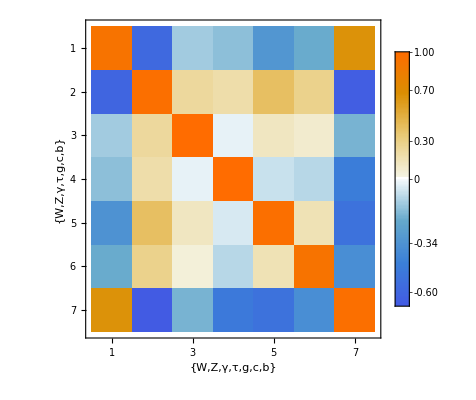

```mathematica
MatrixPlot[%40,FrameLabel->{{"W","Z","γ","τ","g","c","b"},{"W","Z","γ","τ","g","c","b"}},PlotLegends->Automatic]
```

```mathematica
Eigenvalues[%21]
```

{1.45764×10^6,221226.,67099.7,48535.6,30937.8,15919.6,987.163}

### 10p_MI_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2,kz^2 kb^2/ktotal,kz^2 kt^2/ktotal,kz^2 kg^2/ktotal,kz^2 kw^2/ktotal,kz^2 ktau^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kz^2 kmu^2/ktotal,kw^2 kb^2/ktotal,kz^2brinv+1};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100,0.14/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 10p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{10,2.5,1,0.5}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0420525
-0.0403854) | (0.0208194
-0.0204033) | (0.0131192
-0.0129528) | (0.00925944
-0.00917626)
(0.0549682
-0.0530561) | (0.0272377
-0.0267595) | (0.0171701
-0.0169788) | (0.012121
-0.0120254)
(0.0494335
-0.0474334) | (0.0244641
-0.0239643) | (0.015414
-0.0152141) | (0.0108786
-0.0107786)
(0.0387409
-0.0385975) | (0.0193637
-0.0193283) | (0.012244
-0.0122299) | (0.00865667
-0.00864962)
(0.0464184
-0.0444732) | (0.0229652
-0.0224792) | (0.0144679
-0.0142735) | (0.0102101
-0.010113)
(0.00803156
-0.00809659) | (0.00402379
-0.00404005) | (0.00254676
-0.00255326) | (0.0018015
-0.00180475)
(0.14182
-0.157784) | (0.0723428
-0.0762269) | (0.0461336
-0.0476789) | (0.0327644
-0.0335357)
(0.245948
-0.320985) | (0.128651
-0.145883) | (0.082924
-0.0897124) | (0.0592333
-0.0626106)
(0.00442776
-0.00442774) | (0.00221367
-0.00221367) | (0.00140002
-0.00140002) | (0.000989956
-0.000989956)
(0.0910399
-0.0834866) | (0.0445451
-0.0426581) | (0.0279496
-0.0271949) | (0.0196843
-0.019307))

## CDR

### SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

### Defining χ^2 s

```mathematica
(*Following Frederick James P.68-69 for defintions of correlation matrix, covariance matrix, etc.*)
(*inverseinputcorrelations is actually the precision/conentration matrix*)
```

```mathematica
Inverse[{{1,ρ},{ρ,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2)
-ρ/(1-ρ^2) | 1/(1-ρ^2))

```mathematica
Inverse[{{1,ρ,0},{ρ,1,0},{0,0,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2) | 0
-ρ/(1-ρ^2) | 1/(1-ρ^2) | 0
0 | 0 | 1)

```mathematica
inverseinputcorrelations=Inverse[inputcorrelations/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03208 | 0. | 0.178022 | 0.126431 | 0.0000829784 | 0.0000541663 | 0.000663357 | 0.000292187 | 3.08409×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.178022 | 0. | 1.15222 | 0.386438 | 0.059681 | 0.0500988 | 0.00486027 | 0.0000485866 | -4.04817×10^-6 | 0.
0. | 0.126431 | 0. | 0.386438 | 1.13518 | 0.0457993 | 0.0354664 | 0.0243613 | 0.0000328205 | -2.22321×10^-6 | 0.
0. | 0.0000829784 | 0. | 0.059681 | 0.0457993 | 1.07973 | 0.256208 | 0.152045 | -3.46304×10^-6 | 0.0331285 | 0.
0. | 0.0000541663 | 0. | 0.0500988 | 0.0354664 | 0.256208 | 1.07128 | 0.106524 | -3.60363×10^-6 | 0.0727213 | 0.
0. | 0.000663357 | 0. | 0.00486027 | 0.0243613 | 0.152045 | 0.106524 | 1.29084 | 0.577755 | 1.4814×10^-6 | 0.
0. | 0.000292187 | 0. | 0.0000485866 | 0.0000328205 | -3.46304×10^-6 | -3.60363×10^-6 | 0.577755 | 1.26407 | 5.01996×10^-6 | 0.
0. | 3.08409×10^-6 | 0. | -4.04817×10^-6 | -2.22321×10^-6 | 0.0331285 | 0.0727213 | 1.4814×10^-6 | 5.01996×10^-6 | 1.00528 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inverseinputcorrelationslhc7s2=Inverse[inputcorrelationslhc7s2/100];
```

```mathematica
Length[higgsprecepc]
Length[higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau]]
Dimensions[inverseinputcorrelations]
```

11

11

{11,11}

```mathematica
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
(*higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/lumif,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}](*Sum[(higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgsprelhc7s2[[i]]^2,{i,1,Length[higgsprelhc7s2]}]*)
```

```mathematica
chisquarecepc360[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobscepc3607p[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc360[[i]])^2/lumif,{i,1,Length[higgsprecepc360]}]
chisquarecepcL360[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/lumif,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]+Sum[((higgsobscepc3607p[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc360[[i]])^2/lumif,{i,1,Length[higgsprecepc360]}]
```

```mathematica
Length[higgsprelhc7s2]
```

8

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
(*higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};*)
chisquarecepc10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[((higgsobslhc7s2[kz/Sqrt[ktotal],kw/Sqrt[ktotal],kg/Sqrt[ktotal],kgamma/Sqrt[ktotal],kb/Sqrt[ktotal],kt/Sqrt[ktotal],ktau/Sqrt[ktotal],kmu/Sqrt[ktotal]][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz/Sqrt[ktotal],kw/Sqrt[ktotal],kg/Sqrt[ktotal],kgamma/Sqrt[ktotal],kb/Sqrt[ktotal],kt/Sqrt[ktotal],ktau/Sqrt[ktotal],kmu/Sqrt[ktotal]][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/lumif+(kz^2 brinv)^2/0.0235^2,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]
chisquarecepc10p360[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, 0, ktotal][[i]]-1)/higgsprecepc360[[i]])^2/lumif,{i,1,Length[higgsprecepc360]}]
(*higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};*)
chisquarecepc10pL360[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[((higgsobslhc7s2[kz/Sqrt[ktotal],kw/Sqrt[ktotal],kg/Sqrt[ktotal],kgamma/Sqrt[ktotal],kb/Sqrt[ktotal],kt/Sqrt[ktotal],ktau/Sqrt[ktotal],kmu/Sqrt[ktotal]][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz/Sqrt[ktotal],kw/Sqrt[ktotal],kg/Sqrt[ktotal],kgamma/Sqrt[ktotal],kb/Sqrt[ktotal],kt/Sqrt[ktotal],ktau/Sqrt[ktotal],kmu/Sqrt[ktotal]][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/lumif+(kz^2 brinv)^2/0.0235^2,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]+Sum[((higgsobscepc36010p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, 0, ktotal][[i]]-1)/higgsprecepc360[[i]])^2/lumif,{i,1,Length[higgsprecepc360]}]
```

```mathematica
chisquarecepc10pL360[{kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal},1]-chisquarecepc10pL[{kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal},1]//Simplify
```

1/ktotal^2(566.893 kb^4 kgamma^4+493.827 kg^4 kgamma^4+516.529 kgamma^8+3.07787 kgamma^4 kmu^4+25. kt^8+39.0625 kgamma^4 ktau^4-1133.79 kb^2 kgamma^2 ktotal-987.654 kg^2 kgamma^2 ktotal-1033.06 kgamma^4 ktotal-6.15574 kgamma^2 kmu^2 ktotal-78.125 kgamma^2 ktau^2 ktotal+33093.9 ktotal^2-78.125 kgamma^2 ktotal kw^2+39.0625 kgamma^4 kw^4-16528.9 kgamma^2 ktotal kz^2+8264.46 kgamma^4 kz^4-10204.1 kt^2 ktotal (0.479289 kb^2+0.183161 kg^2+0.300835 kgamma^2+0.00116597 kmu^2+0.0161983 ktau^2+1. ktotal+0.0302099 kw^2+2.52576 kz^2)+2445.35 kt^4 (1. kb^4+0.382152 kg^4+0.627669 kgamma^4+0.00243271 kmu^4+0.0337966 ktau^4-0.020447 ktotal+2.08642 ktotal^2+0.0630307 kw^4+5.2698 kz^4))

```mathematica
chisquarecepc10p360[{kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal},1]-chisquarecepc10p[{kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal},1]//Simplify
```

1/ktotal^2(566.893 kb^4 kgamma^4+493.827 kg^4 kgamma^4+516.529 kgamma^8+3.07787 kgamma^4 kmu^4+25. kt^8+39.0625 kgamma^4 ktau^4-1133.79 kb^2 kgamma^2 ktotal-987.654 kg^2 kgamma^2 ktotal-1033.06 kgamma^4 ktotal-6.15574 kgamma^2 kmu^2 ktotal-78.125 kgamma^2 ktau^2 ktotal+33093.9 ktotal^2-78.125 kgamma^2 ktotal kw^2+39.0625 kgamma^4 kw^4-16528.9 kgamma^2 ktotal kz^2+8264.46 kgamma^4 kz^4-10204.1 kt^2 ktotal (0.479289 kb^2+0.183161 kg^2+0.300835 kgamma^2+0.00116597 kmu^2+0.0161983 ktau^2+1. ktotal+0.0302099 kw^2+2.52576 kz^2)+2445.35 kt^4 (1. kb^4+0.382152 kg^4+0.627669 kgamma^4+0.00243271 kmu^4+0.0337966 ktau^4-0.020447 ktotal+2.08642 ktotal^2+0.0630307 kw^4+5.2698 kz^4))

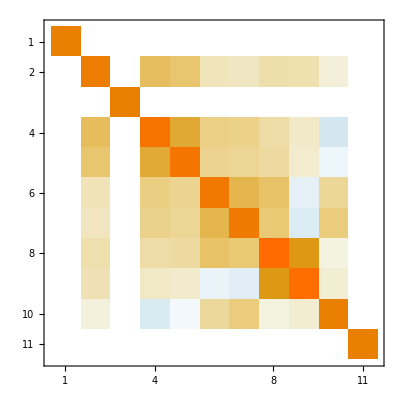

```mathematica
MatrixPlot[inverseinputcorrelations]
```

```mathematica
inverseinputcorrelations//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03208 | 0. | 0.178022 | 0.126431 | 0.0000829784 | 0.0000541663 | 0.000663357 | 0.000292187 | 3.08409×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.178022 | 0. | 1.15222 | 0.386438 | 0.059681 | 0.0500988 | 0.00486027 | 0.0000485866 | -4.04817×10^-6 | 0.
0. | 0.126431 | 0. | 0.386438 | 1.13518 | 0.0457993 | 0.0354664 | 0.0243613 | 0.0000328205 | -2.22321×10^-6 | 0.
0. | 0.0000829784 | 0. | 0.059681 | 0.0457993 | 1.07973 | 0.256208 | 0.152045 | -3.46304×10^-6 | 0.0331285 | 0.
0. | 0.0000541663 | 0. | 0.0500988 | 0.0354664 | 0.256208 | 1.07128 | 0.106524 | -3.60363×10^-6 | 0.0727213 | 0.
0. | 0.000663357 | 0. | 0.00486027 | 0.0243613 | 0.152045 | 0.106524 | 1.29084 | 0.577755 | 1.4814×10^-6 | 0.
0. | 0.000292187 | 0. | 0.0000485866 | 0.0000328205 | -3.46304×10^-6 | -3.60363×10^-6 | 0.577755 | 1.26407 | 5.01996×10^-6 | 0.
0. | 3.08409×10^-6 | 0. | -4.04817×10^-6 | -2.22321×10^-6 | 0.0331285 | 0.0727213 | 1.4814×10^-6 | 5.01996×10^-6 | 1.00528 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inputcorrelations-inputcorrelationsᵀ//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.00685504
-0.00686877)
(0.0128244
-0.0128207)
(0.00866509
-0.00864473)
(0.00741692
-0.00743905)
(0.00757559
-0.00757264)
(0.000668916
-0.000669166)
(0.0167007
-0.016805))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100},3]ᵀ//MatrixForm
```

(kb | {{0.69,-0.69}}
kc | {{1.28,-1.28}}
kg | {{0.87,-0.86}}
kw | {{0.74,-0.74}}
ktau | {{0.76,-0.76}}
kz | {{0.07,-0.07}}
kgamma | {{1.67,-1.68}})

```mathematica
concentrationmatrix7p=Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2;
%//MatrixForm
```

(671873. | -27329.3 | -95456.2 | -252240. | -210314. | 768971. | -4493.76
-27329.3 | 11274.5 | 8098.3 | 6386.79 | -3235.12 | -57947. | 26.6946
-95456.2 | 8098.3 | 69664.1 | 14876.2 | -11842.4 | -162074. | 30.8979
-252240. | 6386.79 | 14876.2 | 206661. | 1825.76 | -419177. | 68.1079
-210314. | -3235.12 | -11842.4 | 1825.76 | 215181. | 48780.1 | -372.373
768971. | -57947. | -162074. | -419177. | 48780.1 | 3.81625×10^6 | -3548.41
-4493.76 | 26.6946 | 30.8979 | 68.1079 | -372.373 | -3548.41 | 4384.66)

```mathematica
covariancematrix7p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7].concentrationmatrix7p.(((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7])];
%//MatrixForm
```

(1.00003 | 0.619746 | 0.88039 | 0.941779 | 0.958123 | -0.382763 | 0.431638
0.619746 | 0.999958 | 0.464678 | 0.581429 | 0.601766 | -0.106254 | 0.269477
0.88039 | 0.464678 | 1.00002 | 0.833463 | 0.853479 | -0.232993 | 0.383271
0.941779 | 0.581429 | 0.833463 | 1.00003 | 0.898795 | -0.220193 | 0.410109
0.958123 | 0.601766 | 0.853479 | 0.898795 | 1.00002 | -0.375013 | 0.416383
-0.382763 | -0.106254 | -0.232993 | -0.220193 | -0.375013 | 0.999999 | -0.139899
0.431638 | 0.269477 | 0.383271 | 0.410109 | 0.416383 | -0.139899 | 0.999803)

```mathematica
correlationmatrix7p=Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]].covariancematrix7p.Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.619751 | 0.88037 | 0.941751 | 0.9581 | -0.382758 | 0.431674
0.619751 | 1. | 0.464683 | 0.581432 | 0.601773 | -0.106256 | 0.26951
0.88037 | 0.464683 | 1. | 0.833442 | 0.853463 | -0.232991 | 0.383305
0.941751 | 0.581432 | 0.833442 | 1. | 0.898772 | -0.220189 | 0.410143
0.9581 | 0.601773 | 0.853463 | 0.898772 | 1. | -0.37501 | 0.41642
-0.382758 | -0.106256 | -0.232991 | -0.220189 | -0.37501 | 1. | -0.139913
0.431674 | 0.26951 | 0.383305 | 0.410143 | 0.41642 | -0.139913 | 1.)

### 7p_fit_CEPC_LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100,cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{0.69,-0.69}} | {{0.69,-0.69}}
kc | {{1.28,-1.28}} | {{1.28,-1.28}}
kg | {{0.87,-0.86}} | {{0.87,-0.86}}
kw | {{0.74,-0.74}} | {{0.74,-0.74}}
ktau | {{0.76,-0.76}} | {{0.76,-0.76}}
kz | {{0.07,-0.07}} | {{0.07,-0.07}}
kgamma | {{1.67,-1.68}} | {{1.67,-1.68}})

```mathematica
CDRresult=SetAccuracy[({{kb, {{1.1802939176687561318`3.0719901691086693,-1.1779947340898035968`3.0711433490581697}}, {{0.9197434346150625828`2.9636666963991947,-0.9172886628042468127`2.962506025893967}}}, {kc, {{2.1133926907131730388`3.32498020105821,-2.1074309458573661225`3.3237533530123526}}, {{1.8618403746730294301`3.269942443900768,-1.8613309632845922437`3.2698236019048914}}}, {kg, {{1.4580201978151960951`3.1637635402638,-1.4470375661800065625`3.160479805875713}}, {{1.1197659218210345156`3.049127246343211,-1.1129849147994486103`3.0464892780240564}}}, {kw, {{1.3065999737734512731`3.1161426451364775,-1.3066112939106404589`3.1161464077661405}}, {{1.0192136691447377661`3.008265239553995,-1.0184521615326214139`3.007940634248957}}}, {ktau, {{1.3353651352430182531`3.1256000331456053,-1.327386804726191194`3.1229974960971303}}, {{1.062794739058968263`3.0264493959421217,-1.0567580318092411051`3.0239755573358593}}}, {kz, {{0.1249436401823528497`2.096714154788162,-0.125110532339467978`2.0972938719985508}}, {{0.1210227905475330101`2.0828671626884825,-0.1211510064978167656`2.0833270265183628}}}, {kgamma, {{3.6111055639962503783`3.5576401844088106,-3.6868600986080872772`3.5666566582040904}}, {{1.6058221714330700447`3.2056974498832576,-1.6096675187487814451`3.2067361805757737}}}}),3]//MatrixForm
```

(kb | {{1.18,-1.18}} | {{0.92,-0.92}}
kc | {{2.11,-2.11}} | {{1.86,-1.86}}
kg | {{1.46,-1.45}} | {{1.12,-1.11}}
kw | {{1.31,-1.31}} | {{1.02,-1.02}}
ktau | {{1.34,-1.33}} | {{1.06,-1.06}}
kz | {{0.12,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.61,-3.69}} | {{1.61,-1.61}})

```mathematica
concentrationmatrix7pL=Table[D[chisquarecepcL[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2
```

{{671873.,-27329.3,-95456.2,-252240.,-210314.,768971.,-4493.78},{-27329.3,11274.8,8098.24,6386.58,-3235.24,-57947.1,26.5133},{-95456.2,8098.24,69664.7,14876.,-11842.4,-162074.,30.9569},{-252240.,6386.58,14876.,206662.,1825.74,-419177.,68.1598},{-210314.,-3235.24,-11842.4,1825.74,215181.,48779.9,-372.381},{768971.,-57947.1,-162074.,-419177.,48779.9,3.81626×10^6,-3548.34},{-4493.78,26.5133,30.9569,68.1598,-372.381,-3548.34,4384.99}}

```mathematica
covariancematrix7pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7].concentrationmatrix7pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7])];
%//MatrixForm
```

(1.00003 | 0.619749 | 0.880382 | 0.941772 | 0.958119 | -0.382753 | 0.431621
0.619749 | 0.999958 | 0.464677 | 0.581431 | 0.601769 | -0.106248 | 0.269489
0.880382 | 0.464677 | 1.00002 | 0.833452 | 0.853471 | -0.232978 | 0.383249
0.941772 | 0.581431 | 0.833452 | 1.00003 | 0.898787 | -0.220177 | 0.410091
0.958119 | 0.601769 | 0.853471 | 0.898787 | 1.00002 | -0.375003 | 0.416367
-0.382753 | -0.106248 | -0.232978 | -0.220177 | -0.375003 | 0.999999 | -0.139888
0.431621 | 0.269489 | 0.383249 | 0.410091 | 0.416367 | -0.139888 | 0.999802)

```mathematica
correlationmatrix7pL=Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]].covariancematrix7pL.Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.619755 | 0.880363 | 0.941747 | 0.958097 | -0.382749 | 0.431658
0.619755 | 1. | 0.464683 | 0.581435 | 0.601776 | -0.10625 | 0.269522
0.880363 | 0.464683 | 1. | 0.833433 | 0.853455 | -0.232976 | 0.383284
0.941747 | 0.581435 | 0.833433 | 1. | 0.898766 | -0.220174 | 0.410126
0.958097 | 0.601776 | 0.853455 | 0.898766 | 1. | -0.375 | 0.416404
-0.382749 | -0.10625 | -0.232976 | -0.220174 | -0.375 | 1. | -0.139901
0.431658 | 0.269522 | 0.383284 | 0.410126 | 0.416404 | -0.139901 | 1.)

### 7p_fit_CEPC w 360

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p360=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc360[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc360[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p360//MatrixForm
```

((0.00414794
-0.00415003)
(0.0108963
-0.0109391)
(0.00605064
-0.00604065)
(0.00416478
-0.00417753)
(0.00489047
-0.00488368)
(0.000642125
-0.000642461)
(0.0148789
-0.015036))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p360*100},3]ᵀ//MatrixForm
```

(kb | {{0.41,-0.42}}
kc | {{1.09,-1.09}}
kg | {{0.61,-0.6}}
kw | {{0.42,-0.42}}
ktau | {{0.49,-0.49}}
kz | {{0.06,-0.06}}
kgamma | {{1.49,-1.5}})

### 7p_fit_CEPC_LHC w 360

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL360=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL360[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL360[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p360*100,cepc7pL360*100},3]ᵀ//MatrixForm
```

(kb | {{0.41,-0.42}} | {{0.41,-0.41}}
kc | {{1.09,-1.09}} | {{1.09,-1.09}}
kg | {{0.61,-0.6}} | {{0.61,-0.6}}
kw | {{0.42,-0.42}} | {{0.42,-0.42}}
ktau | {{0.49,-0.49}} | {{0.49,-0.49}}
kz | {{0.06,-0.06}} | {{0.06,-0.06}}
kgamma | {{1.49,-1.5}} | {{1.49,-1.5}})

```mathematica
CDRresult=SetAccuracy[({{kb, {{1.1802939176687561318`3.0719901691086693,-1.1779947340898035968`3.0711433490581697}}, {{0.9197434346150625828`2.9636666963991947,-0.9172886628042468127`2.962506025893967}}}, {kc, {{2.1133926907131730388`3.32498020105821,-2.1074309458573661225`3.3237533530123526}}, {{1.8618403746730294301`3.269942443900768,-1.8613309632845922437`3.2698236019048914}}}, {kg, {{1.4580201978151960951`3.1637635402638,-1.4470375661800065625`3.160479805875713}}, {{1.1197659218210345156`3.049127246343211,-1.1129849147994486103`3.0464892780240564}}}, {kw, {{1.3065999737734512731`3.1161426451364775,-1.3066112939106404589`3.1161464077661405}}, {{1.0192136691447377661`3.008265239553995,-1.0184521615326214139`3.007940634248957}}}, {ktau, {{1.3353651352430182531`3.1256000331456053,-1.327386804726191194`3.1229974960971303}}, {{1.062794739058968263`3.0264493959421217,-1.0567580318092411051`3.0239755573358593}}}, {kz, {{0.1249436401823528497`2.096714154788162,-0.125110532339467978`2.0972938719985508}}, {{0.1210227905475330101`2.0828671626884825,-0.1211510064978167656`2.0833270265183628}}}, {kgamma, {{3.6111055639962503783`3.5576401844088106,-3.6868600986080872772`3.5666566582040904}}, {{1.6058221714330700447`3.2056974498832576,-1.6096675187487814451`3.2067361805757737}}}}),3]//MatrixForm
```

(kb | {{1.18,-1.18}} | {{0.92,-0.92}}
kc | {{2.11,-2.11}} | {{1.86,-1.86}}
kg | {{1.46,-1.45}} | {{1.12,-1.11}}
kw | {{1.31,-1.31}} | {{1.02,-1.02}}
ktau | {{1.34,-1.33}} | {{1.06,-1.06}}
kz | {{0.12,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.61,-3.69}} | {{1.61,-1.61}})

### 10p-fit-CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.007525
-0.00752853)
(0.0130418
-0.0130248)
(0.00908825
-0.0090604)
(0.00782791
-0.00784561)
(0.00823898
-0.0082259)
(0.00129916
-0.00130085)
(0.0169645
-0.0170475)
(0.0323445
-0.0330346)
(0.000700002
-0.0007)
(0.0163486
-0.0161963))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100},3]ᵀ//MatrixForm
```

(kb | {{0.75,-0.75}}
kt | {{1.3,-1.3}}
kg | {{0.91,-0.91}}
kw | {{0.78,-0.78}}
ktau | {{0.82,-0.82}}
kz | {{0.13,-0.13}}
kgamma | {{1.7,-1.7}}
kmu | {{3.23,-3.3}}
brinv | {{0.07,-0.07}}
ktotal | {{1.63,-1.62}})

```mathematica
concentrationmatrix10p=Table[D[chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10].concentrationmatrix10p.(((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10])];
%//MatrixForm
```

(1.00002 | 0.629464 | 0.889009 | 0.944782 | 0.964508 | 0.172717 | 0.458287 | 0.238413 | 0. | 0.98549
0.629464 | 0.999961 | 0.489856 | 0.599275 | 0.614826 | 0.0997445 | 0.29196 | 0.151886 | 0. | 0.626181
0.889009 | 0.489856 | 1.00001 | 0.849256 | 0.86659 | 0.143261 | 0.411769 | 0.214213 | 0. | 0.883553
0.944782 | 0.599275 | 0.849256 | 1.00003 | 0.908529 | 0.165885 | 0.43772 | 0.227714 | 0. | 0.941411
0.964508 | 0.614826 | 0.86659 | 0.908529 | 1.00001 | 0.157912 | 0.444679 | 0.231334 | 0. | 0.954682
0.172717 | 0.0997445 | 0.143261 | 0.165885 | 0.157912 | 0.999998 | 0.0764435 | 0.039768 | 0. | 0.319559
0.458287 | 0.29196 | 0.411769 | 0.43772 | 0.444679 | 0.0764435 | 0.999806 | 0.109977 | 0. | 0.454078
0.238413 | 0.151886 | 0.214213 | 0.227714 | 0.231334 | 0.039768 | 0.109977 | 1.00353 | 0. | 0.236224
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999996 | 0.
0.98549 | 0.626181 | 0.883553 | 0.941411 | 0.954682 | 0.319559 | 0.454078 | 0.236224 | 0. | 1.00016)

```mathematica
correlationmatrix10p=Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]].covariancematrix10p.Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.62947 | 0.888994 | 0.94476 | 0.964493 | 0.172715 | 0.458327 | 0.237992 | 0. | 0.985404
0.62947 | 1. | 0.489861 | 0.599278 | 0.614833 | 0.0997465 | 0.291994 | 0.151621 | 0. | 0.626145
0.888994 | 0.489861 | 1. | 0.849237 | 0.866578 | 0.14326 | 0.411805 | 0.213835 | 0. | 0.883478
0.94476 | 0.599278 | 0.849237 | 1. | 0.90851 | 0.165883 | 0.437756 | 0.22731 | 0. | 0.941324
0.964493 | 0.614833 | 0.866578 | 0.90851 | 1. | 0.157911 | 0.444719 | 0.230926 | 0. | 0.954601
0.172715 | 0.0997465 | 0.14326 | 0.165883 | 0.157911 | 1. | 0.076451 | 0.0396981 | 0. | 0.319534
0.458327 | 0.291994 | 0.411805 | 0.437756 | 0.444719 | 0.076451 | 1. | 0.109794 | 0. | 0.454087
0.237992 | 0.151621 | 0.213835 | 0.22731 | 0.230926 | 0.0396981 | 0.109794 | 1. | 0. | 0.23579
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.985404 | 0.626145 | 0.883478 | 0.941324 | 0.954601 | 0.319534 | 0.454087 | 0.23579 | 0. | 1.)

### 10p-fit-CEPC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL//MatrixForm
```

((0.00752487
-0.00752838)
(0.0130415
-0.0130245)
(0.00908808
-0.00906026)
(0.00782777
-0.00784547)
(0.00823883
-0.00822575)
(0.00129916
-0.00130084)
(0.016964
-0.017047)
(0.0323438
-0.0330332)
(0.000680934
-0.000680934)
(0.0163508
-0.016196))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},4]ᵀ//MatrixForm
```

(kb | {{0.753,-0.753}} | {{0.752,-0.753}}
kt | {{1.304,-1.302}} | {{1.304,-1.302}}
kg | {{0.909,-0.906}} | {{0.909,-0.906}}
kw | {{0.783,-0.785}} | {{0.783,-0.785}}
ktau | {{0.824,-0.823}} | {{0.824,-0.823}}
kz | {{0.13,-0.13}} | {{0.13,-0.13}}
kgamma | {{1.696,-1.705}} | {{1.696,-1.705}}
kmu | {{3.234,-3.303}} | {{3.234,-3.303}}
brinv | {{0.07,-0.07}} | {{0.068,-0.068}}
ktotal | {{1.635,-1.62}} | {{1.635,-1.62}})

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{0.75,-0.75}} | {{0.75,-0.75}}
kt | {{1.3,-1.3}} | {{1.3,-1.3}}
kg | {{0.91,-0.91}} | {{0.91,-0.91}}
kw | {{0.78,-0.78}} | {{0.78,-0.78}}
ktau | {{0.82,-0.82}} | {{0.82,-0.82}}
kz | {{0.13,-0.13}} | {{0.13,-0.13}}
kgamma | {{1.7,-1.7}} | {{1.7,-1.7}}
kmu | {{3.23,-3.3}} | {{3.23,-3.3}}
brinv | {{0.07,-0.07}} | {{0.07,-0.07}}
ktotal | {{1.63,-1.62}} | {{1.64,-1.62}})

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL},2]ᵀ//MatrixForm
```

(kb | 0.8 | 0.8
kt | 1.3 | 1.3
kg | 0.9 | 0.9
kw | 0.8 | 0.8
ktau | 0.8 | 0.8
kz | 0.1 | 0.1
kgamma | 1.7 | 1.7
kmu | 3.3 | 3.3
brinv | 0.07 | 0.07
ktotal | 1.6 | 1.6)

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.00752676,0.0130333,0.00907433,0.00783676,0.00823244,0.0013,0.017006,0.0326896,0.000700001,0.0162724}

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.00752676,0.0130333,0.00907433,0.00783676,0.00823244,0.0013,0.017006,0.0326896,0.000700001,0.0162724}

```mathematica
concentrationmatrix10pL=Table[D[chisquarecepc10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10].concentrationmatrix10pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10])];
%//MatrixForm
```

(1.00002 | 0.62946 | 0.889007 | 0.94478 | 0.964508 | 0.172718 | 0.458301 | 0.238415 | 0. | 0.985415
0.62946 | 0.999962 | 0.489852 | 0.599271 | 0.614821 | 0.0997414 | 0.291986 | 0.151887 | 0. | 0.626128
0.889007 | 0.489852 | 1.00002 | 0.849252 | 0.866588 | 0.143263 | 0.411776 | 0.214214 | 0. | 0.883484
0.94478 | 0.599271 | 0.849252 | 1.00003 | 0.908526 | 0.165886 | 0.437732 | 0.227715 | 0. | 0.941338
0.964508 | 0.614821 | 0.866588 | 0.908526 | 1.00001 | 0.157913 | 0.444692 | 0.231335 | 0. | 0.954608
0.172718 | 0.0997414 | 0.143263 | 0.165886 | 0.157913 | 0.999998 | 0.0764501 | 0.0397694 | 0. | 0.319538
0.458301 | 0.291986 | 0.411776 | 0.437732 | 0.444692 | 0.0764501 | 0.999806 | 0.109977 | 0. | 0.454058
0.238415 | 0.151887 | 0.214214 | 0.227715 | 0.231335 | 0.0397694 | 0.109977 | 1.00355 | 0. | 0.236207
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999999 | 0.
0.985415 | 0.626128 | 0.883484 | 0.941338 | 0.954608 | 0.319538 | 0.454058 | 0.236207 | 0. | 1.)

```mathematica
Sqrt[Diagonal[covariancematrix10pL]]
```

{1.00001,0.999981,1.00001,1.00001,1.00001,0.999999,0.999903,1.00177,1.,1.}

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.629466 | 0.888992 | 0.944758 | 0.964492 | 0.172717 | 0.458341 | 0.237991 | 0. | 0.985404
0.629466 | 1. | 0.489857 | 0.599274 | 0.614829 | 0.0997433 | 0.29202 | 0.151621 | 0. | 0.626139
0.888992 | 0.489857 | 1. | 0.849234 | 0.866575 | 0.143262 | 0.411813 | 0.213833 | 0. | 0.883476
0.944758 | 0.599274 | 0.849234 | 1. | 0.908507 | 0.165884 | 0.437768 | 0.227309 | 0. | 0.941323
0.964492 | 0.614829 | 0.866575 | 0.908507 | 1. | 0.157912 | 0.444732 | 0.230924 | 0. | 0.9546
0.172717 | 0.0997433 | 0.143262 | 0.165884 | 0.157912 | 1. | 0.0764576 | 0.039699 | 0. | 0.319538
0.458341 | 0.29202 | 0.411813 | 0.437768 | 0.444732 | 0.0764576 | 1. | 0.109793 | 0. | 0.454101
0.237991 | 0.151621 | 0.213833 | 0.227309 | 0.230924 | 0.039699 | 0.109793 | 1. | 0. | 0.235789
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.985404 | 0.626139 | 0.883476 | 0.941323 | 0.9546 | 0.319538 | 0.454101 | 0.235789 | 0. | 1.)

```mathematica
correlationmatrix10pL//MatrixForm
```

(1. | 0.629466 | 0.888992 | 0.944758 | 0.964492 | 0.172717 | 0.458341 | 0.237991 | 0. | 0.985404
0.629466 | 1. | 0.489857 | 0.599274 | 0.614829 | 0.0997433 | 0.29202 | 0.151621 | 0. | 0.626139
0.888992 | 0.489857 | 1. | 0.849234 | 0.866575 | 0.143262 | 0.411813 | 0.213833 | 0. | 0.883476
0.944758 | 0.599274 | 0.849234 | 1. | 0.908507 | 0.165884 | 0.437768 | 0.227309 | 0. | 0.941323
0.964492 | 0.614829 | 0.866575 | 0.908507 | 1. | 0.157912 | 0.444732 | 0.230924 | 0. | 0.9546
0.172717 | 0.0997433 | 0.143262 | 0.165884 | 0.157912 | 1. | 0.0764576 | 0.039699 | 0. | 0.319538
0.458341 | 0.29202 | 0.411813 | 0.437768 | 0.444732 | 0.0764576 | 1. | 0.109793 | 0. | 0.454101
0.237991 | 0.151621 | 0.213833 | 0.227309 | 0.230924 | 0.039699 | 0.109793 | 1. | 0. | 0.235789
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.985404 | 0.626139 | 0.883476 | 0.941323 | 0.9546 | 0.319538 | 0.454101 | 0.235789 | 0. | 1.)

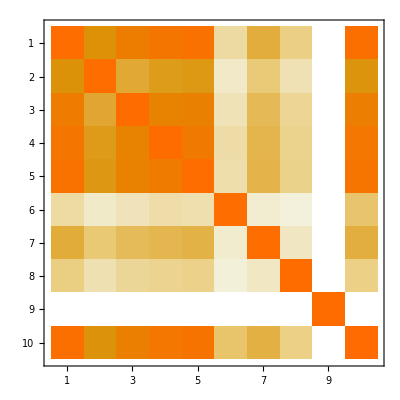

```mathematica
MatrixPlot[correlationmatrix10pL]
```

### 10p-fit-CEPC w 360

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p360=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p360[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p360[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p360//MatrixForm
```

((0.00476349
-0.00475674)
(0.0110072
-0.0110402)
(0.00635225
-0.00633511)
(0.00449115
-0.00449955)
(0.00546344
-0.00544824)
(0.00127733
-0.00127896)
(0.0150389
-0.0151815)
(0.0311748
-0.0319933)
(0.000700002
-0.0007)
(0.0108259
-0.0107389))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p360*100},3]ᵀ//MatrixForm
```

(kb | {{0.48,-0.48}}
kt | {{1.1,-1.1}}
kg | {{0.64,-0.63}}
kw | {{0.45,-0.45}}
ktau | {{0.55,-0.54}}
kz | {{0.13,-0.13}}
kgamma | {{1.5,-1.52}}
kmu | {{3.12,-3.2}}
brinv | {{0.07,-0.07}}
ktotal | {{1.08,-1.07}})

### 10p-fit-CEPC-LHC w 360

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL360=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL360[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL360[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2,ktotal(1-brinv)≥ kh[kz,kw,kg,kgamma,kb,kt,ktau]},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL360//MatrixForm
```

((0.00476339
-0.00475671)
(0.0110069
-0.01104)
(0.00635221
-0.00633506)
(0.00449113
-0.00449954)
(0.0054634
-0.0054482)
(0.00127733
-0.00127896)
(0.0150384
-0.015181)
(0.0311741
-0.0319926)
(0.000680934
-0.000680934)
(0.0108259
-0.0107388))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p360,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL360},4]ᵀ//MatrixForm
```

(kb | 0.753 | 0.753 | 0.476 | 0.476
kt | 1.303 | 1.303 | 1.102 | 1.102
kg | 0.907 | 0.907 | 0.634 | 0.634
kw | 0.784 | 0.784 | 0.45 | 0.45
ktau | 0.823 | 0.823 | 0.546 | 0.546
kz | 0.13 | 0.13 | 0.128 | 0.128
kgamma | 1.701 | 1.701 | 1.511 | 1.511
kmu | 3.269 | 3.269 | 3.158 | 3.158
brinv | 0.07 | 0.068 | 0.07 | 0.068
ktotal | 1.627 | 1.627 | 1.078 | 1.078)

Result without correlation -Graphics-

{0.00788396,0.0128268,0.0088833,0.00757328,0.00818049,0.00129992,0.0170463,0.0327191,0.000700001,0.0164415}

```mathematica
({{kb, 0.7526764831761274532`3.876608347034153, 0.7526624983916843092`3.8766002777357573, 0.4760114154399100461`3.6776173678530877, 0.476004874164318359`3.6776113998041686}, {kt, 1.3033290282917042724`4.1150540681553, 1.3033010660906996225`4.115044750508255, 1.1023666074023692474`4.042326049229249, 1.1023467364648524836`4.042318220693591}, {kg, 0.9074326487506942929`3.9578144008030267, 0.9074167756495794546`3.9578068039190843, 0.634367969165671286`3.8023412462424133, 0.6343635356081335219`3.802338210975193}, {kw, 0.7836756724668026974`3.8941363652349206, 0.783662263123872771`3.8941289340313388, 0.4495349618683302517`3.65276347394696, 0.4495336755094028192`3.6527622311973835}, {ktau, 0.8232437562691586885`3.915528445575098, 0.8232286885562527523`3.9155204966724715, 0.5455840102211959586`3.7368616336893674, 0.5455802548424328879`3.7368586443314373}, {kz, 0.1300001046341718036`3.1139437018608764, 0.1299999998715501426`3.1139433518777206, 0.1278146382157261951`3.106580595076373, 0.127814538126062166`3.106580254986956}, {kgamma, 1.7006010263442778996`4.230602436845389, 1.7005513020478140174`4.230589738215344, 1.5110174270783174322`4.179269473233998, 1.5109719632484666096`4.179256405888034}, {kmu, 3.2689554681634716005`4.5144090043789, 3.2688502610332244025`4.514395026944262, 3.1584046458220536024`4.499467769810908, 3.158333647574104841`4.4994580071309045}, {brinv, 0.0700001327649586863`2.8450988637147465, 0.068093353210161231`2.833104721236829, 0.0700001261865877134`2.8450988229012473, 0.0680933608981838107`2.8331047702704786}, {ktotal, 1.6272430397749841902`4.2114524226052055, 1.6273388215931237077`4.211477985038027, 1.0782408240726297777`4.032715770948219, 1.0782340580030187471`4.032713045698117}})
```

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.00752676,0.0130333,0.00907433,0.00783676,0.00823244,0.0013,0.017006,0.0326896,0.000700001,0.0162724}

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma},(#[[1,1]]-#[[1,2]])/2*100&/@cepc7p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc7pL,(#[[1,1]]-#[[1,2]])/2*100&/@cepc7p360,(#[[1,1]]-#[[1,2]])/2*100&/@cepc7pL360},4]ᵀ//MatrixForm
```

(kb | 0.734 | 0.733 | 0.444 | 0.444
kt | 1.276 | 1.276 | 1.09 | 1.09
kg | 0.861 | 0.861 | 0.606 | 0.606
kw | 0.73 | 0.73 | 0.411 | 0.411
ktau | 0.765 | 0.765 | 0.488 | 0.488
kz | 0.074 | 0.074 | 0.072 | 0.072
kgamma | 1.682 | 1.682 | 1.499 | 1.499)

```mathematica
({{kb, 0.7335115142042618608`3.865406935515534, 0.733488439863744901`3.865393273539972, 0.444110474788324272`3.647491016562822, 0.4441064335651934702`3.647487064643219}, {kt, 1.2755453631377069446`4.105695908347662, 1.2755302048163601469`4.105690747249811, 1.0904884888990022951`4.037621085564394, 1.0904790704987468164`4.037617334606026}, {kg, 0.860918115064170042`3.934961846149416, 0.8608908447153569288`3.9349480892666406, 0.6059616707074007014`3.782445154320203, 0.6059543169674824759`3.782439883841555}, {kw, 0.7295664153561978171`3.8630648335972375, 0.7295415170356408519`3.863050011933963, 0.4108533179187128237`3.6136867985457872, 0.4108494382256114852`3.6136826974781133}, {ktau, 0.764875804307784346`3.8835909228888026, 0.7648506774621601778`3.883576655697205, 0.4883107913604829986`3.688696322024291, 0.4883054956032676364`3.6886916120513633}, {kz, 0.0744548585861120743`2.8718930430994836, 0.0744546599922774888`2.8718918847019905, 0.0723577075594627195`2.859484799066072, 0.0723577134986372744`2.8594848347132853}, {kgamma, 1.6823925803069954554`4.225927344355609, 1.6823185373833136058`4.225908230421569, 1.4994643910001566045`4.175936156673896, 1.4994111798735136887`4.175920744698218}})
```

(kb | 0.686 | 0.686 | 0.415 | 0.415
kt | 1.282 | 1.282 | 1.092 | 1.092
kg | 0.865 | 0.865 | 0.605 | 0.605
kw | 0.743 | 0.743 | 0.417 | 0.417
ktau | 0.757 | 0.757 | 0.489 | 0.489
kz | 0.067 | 0.067 | 0.064 | 0.064
kgamma | 1.675 | 1.675 | 1.496 | 1.496)

(kb | 0.073 | 0.073 | 0.073 | 0.073
kt | 0.128 | 0.128 | 0.127 | 0.127
kg | 0.086 | 0.086 | 0.085 | 0.085
kw | 0.073 | 0.073 | 0.072 | 0.072
ktau | 0.076 | 0.076 | 0.076 | 0.076
kz | 0.007 | 0.007 | 0.007 | 0.007
kgamma | 0.168 | 0.168 | 0.168 | 0.168)

(kb | 0.073 | 0.073 | 0.073 | 0.073
kt | 0.128 | 0.128 | 0.127 | 0.127
kg | 0.086 | 0.086 | 0.085 | 0.085
kw | 0.073 | 0.073 | 0.072 | 0.072
ktau | 0.076 | 0.076 | 0.076 | 0.076
kz | 0.007 | 0.007 | 0.007 | 0.007
kgamma | 0.168 | 0.168 | 0.168 | 0.168)

(kb | 0.073 | 0.073 | 0.073 | 0.073
kt | 0.128 | 0.128 | 0.127 | 0.127
kg | 0.086 | 0.086 | 0.085 | 0.085
kw | 0.073 | 0.073 | 0.072 | 0.072
ktau | 0.076 | 0.076 | 0.076 | 0.076
kz | 0.007 | 0.007 | 0.007 | 0.007
kgamma | 0.168 | 0.168 | 0.168 | 0.168)

«3 more identical outputs»

(kb | 0.734 | 0.733 | 0.444 | 0.444
kt | 1.276 | 1.276 | 1.09 | 1.09
kg | 0.861 | 0.861 | 0.606 | 0.606
kw | 0.73 | 0.73 | 0.411 | 0.411
ktau | 0.765 | 0.765 | 0.488 | 0.488
kz | 0.074 | 0.074 | 0.072 | 0.072
kgamma | 1.682 | 1.682 | 1.499 | 1.499)

(kb | 0.686 | 0.686 | 0.415 | 0.415
kt | 1.282 | 1.282 | 1.092 | 1.092
kg | 0.865 | 0.865 | 0.605 | 0.605
kw | 0.743 | 0.743 | 0.417 | 0.417
ktau | 0.757 | 0.757 | 0.489 | 0.489
kz | 0.067 | 0.067 | 0.064 | 0.064
kgamma | 1.675 | 1.675 | 1.496 | 1.496)

(kb | 0.686 | 0.686 | 0.415 | 0.415
kt | 1.282 | 1.282 | 1.092 | 1.092
kg | 0.865 | 0.865 | 0.605 | 0.605
kw | 0.743 | 0.743 | 0.417 | 0.417
ktau | 0.757 | 0.757 | 0.489 | 0.489
kz | 0.067 | 0.067 | 0.064 | 0.064
kgamma | 1.675 | 1.675 | 1.496 | 1.496)

Result without correlation-Graphics-

## Supplementals

CDR (width subchannel ZZ)

```mathematica
(*It is triky now to define subchannel fit; there are two approaches, which might cause confusion, I list them here*)
(*1: freeze all the other measurements/parameters, techinically means we set the precision to infinity for iirelevant channels; this will first improve a given cross section measurement, then we combine. In other words, the fit input precision will change for the relevant channels. It then will be hard to combine different channels as they will correspond to different degree of freedoms.*)
(*2: use the same input precision but remove the correlation entries with irrelavant ones, then calculate. This avoids the problem above. I will take the second approach.*)
```

```mathematica
higgsprecepcoriginal=higgsprecepc
```

{0.171,0.0082,0.0684,0.0098,0.0509,0.0127,0.0326,0.003068,0.029991,∞,0.005}

```mathematica
higgsprecepc=Table[If[i==5||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,∞,0.0509,∞,∞,∞,∞,∞,0.005}

```mathematica
inputcorrelationsoriginal=inputcorrelations;
```

```mathematica
inverseinputcorrelations=Inverse[(IdentityMatrix[11]*100+SparseArray[{{11,11}->0,{5,11}->inputcorrelationsoriginal[[5,11]]}]+SparseArray[{{11,11}->0,{5,11}->inputcorrelationsoriginal[[5,11]]}]ᵀ)/100]
```

{{1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={Infinity,Infinity,Infinity,Infinity,5.07,Infinity,Infinity,Infinity,Infinity,Infinity,0.5}/100;
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+40000. (-1+kz^2)^2+389.031 (-1+kz^4/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[%,kz][[1]]},{x,-0.2,0.2,0.002}]
```

{{-0.2,22.9286},{-0.198,22.3667},{-0.196,21.8142},{-0.194,21.2712},{-0.192,20.7376},{-0.19,20.2131},{-0.188,19.6978},{-0.186,19.1914},{-0.184,18.6939},{-0.182,18.2052},{-0.18,17.7252},{-0.178,17.2537},{-0.176,16.7907},{-0.174,16.3361},{-0.172,15.8898},{-0.17,15.4516},{-0.168,15.0215},{-0.166,14.5993},{-0.164,14.1851},{-0.162,13.7786},{-0.16,13.3799},{-0.158,12.9887},{-0.156,12.6051},{-0.154,12.2289},{-0.152,11.86},{-0.15,11.4984},{-0.148,11.1439},{-0.146,10.7966},{-0.144,10.4562},{-0.142,10.1228},{-0.14,9.79615},{-0.138,9.4763},{-0.136,9.16313},{-0.134,8.85655},{-0.132,8.5565},{-0.13,8.2629},{-0.128,7.97566},{-0.126,7.69473},{-0.124,7.42001},{-0.122,7.15145},{-0.12,6.88896},{-0.118,6.63248},{-0.116,6.38194},{-0.114,6.13726},{-0.112,5.89839},{-0.11,5.66525},{-0.108,5.43777},{-0.106,5.2159},{-0.104,4.99956},{-0.102,4.78869},{-0.1,4.58323},{-0.098,4.38311},{-0.096,4.18828},{-0.094,3.99866},{-0.092,3.81421},{-0.09,3.63486},{-0.088,3.46055},{-0.086,3.29123},{-0.084,3.12683},{-0.082,2.9673},{-0.08,2.81258},{-0.078,2.66263},{-0.076,2.51737},{-0.074,2.37676},{-0.072,2.24075},{-0.07,2.10928},{-0.068,1.9823},{-0.066,1.85976},{-0.064,1.7416},{-0.062,1.62778},{-0.06,1.51825},{-0.058,1.41295},{-0.056,1.31184},{-0.054,1.21487},{-0.052,1.12199},{-0.05,1.03316},{-0.048,0.948325},{-0.046,0.867444},{-0.044,0.790471},{-0.042,0.71736},{-0.04,0.648066},{-0.038,0.582547},{-0.036,0.520759},{-0.034,0.462659},{-0.032,0.408204},{-0.03,0.357354},{-0.028,0.310065},{-0.026,0.266298},{-0.024,0.226012},{-0.022,0.189167},{-0.02,0.155723},{-0.018,0.125642},{-0.016,0.0988852},{-0.014,0.0754138},{-0.012,0.0551905},{-0.01,0.0381779},{-0.008,0.0243391},{-0.006,0.0136378},{-0.004,0.00603783},{-0.002,0.00150364},{0.,0.},{0.002,0.0014921},{0.004,0.00594552},{0.006,0.0133262},{0.008,0.0236006},{0.01,0.0367353},{0.012,0.0526976},{0.014,0.0714548},{0.016,0.0929748},{0.018,0.117226},{0.02,0.144177},{0.022,0.173796},{0.024,0.206053},{0.026,0.240918},{0.028,0.278359},{0.03,0.318349},{0.032,0.360857},{0.034,0.405854},{0.036,0.453312},{0.038,0.503202},{0.04,0.555495},{0.042,0.610166},{0.044,0.667185},{0.046,0.726525},{0.048,0.788161},{0.05,0.852064},{0.052,0.91821},{0.054,0.986572},{0.056,1.05712},{0.058,1.12984},{0.06,1.2047},{0.062,1.28167},{0.064,1.36073},{0.066,1.44186},{0.068,1.52503},{0.07,1.61022},{0.072,1.6974},{0.074,1.78655},{0.076,1.87766},{0.078,1.97068},{0.08,2.06562},{0.082,2.16243},{0.084,2.2611},{0.086,2.36161},{0.088,2.46393},{0.09,2.56805},{0.092,2.67394},{0.094,2.78159},{0.096,2.89096},{0.098,3.00205},{0.1,3.11483},{0.102,3.22928},{0.104,3.34538},{0.106,3.46311},{0.108,3.58246},{0.11,3.7034},{0.112,3.82591},{0.114,3.94998},{0.116,4.07559},{0.118,4.20272},{0.12,4.33134},{0.122,4.46145},{0.124,4.59303},{0.126,4.72605},{0.128,4.86051},{0.13,4.99638},{0.132,5.13364},{0.134,5.27228},{0.136,5.41229},{0.138,5.55364},{0.14,5.69633},{0.142,5.84033},{0.144,5.98562},{0.146,6.1322},{0.148,6.28005},{0.15,6.42914},{0.152,6.57948},{0.154,6.73103},{0.156,6.88379},{0.158,7.03775},{0.16,7.19288},{0.162,7.34917},{0.164,7.50661},{0.166,7.66518},{0.168,7.82488},{0.17,7.98568},{0.172,8.14757},{0.174,8.31054},{0.176,8.47458},{0.178,8.63967},{0.18,8.80579},{0.182,8.97295},{0.184,9.14111},{0.186,9.31028},{0.188,9.48044},{0.19,9.65157},{0.192,9.82366},{0.194,9.9967},{0.196,10.1707},{0.198,10.3456},{0.2,10.5214}}

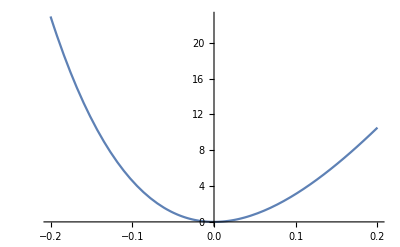

{{x→0.0543855}}

```mathematica
Plot[Interpolation[tempdata][x],{x,-0.2,0.2}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

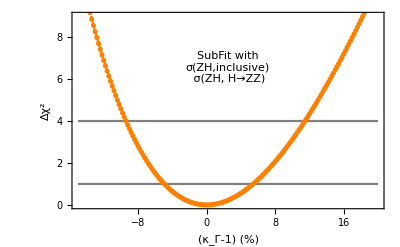

{{x→0.0543855}}

```mathematica
Show[Plot[{Interpolation[tempdata][x/100],1,4},{x,-0.15*100,0.2*100},PlotRange->{0,9},Frame->True,FrameLabel->{"(κ_Γ-1) (%)","Δχ^2"},BaseStyle->16,PlotStyle->{Orange,Gray,Gray}],ListPlot[{#[[1]]*100,#[[2]]}&/@tempdata,PlotStyle->Orange],Epilog->Inset[Framed[Style["SubFit with\nσ(ZH,inclusive)\n σ(ZH, H→ZZ)",13],FrameStyle->None,Background->White],Scaled[{0.5,0.72}]]]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

CDR (width subchannel WW)

```mathematica
higgsprecepc=Table[If[i==4||i==8||i==9||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,0.0098,∞,∞,∞,0.003068,0.029991,∞,0.005}

```mathematica
inverseinputcorrelations=Inverse[(IdentityMatrix[11]*100+SparseArray[{{11,11}->0,{4,8}->inputcorrelationsoriginal[[4,8]],{4,9}->inputcorrelationsoriginal[[4,9]],{4,11}->inputcorrelationsoriginal[[4,11]],{8,9}->inputcorrelationsoriginal[[8,9]],{8,11}->inputcorrelationsoriginal[[8,11]],{9,11}->inputcorrelationsoriginal[[9,11]]}]+SparseArray[{{11,11}->0,{4,8}->inputcorrelationsoriginal[[4,8]],{4,9}->inputcorrelationsoriginal[[4,9]],{4,11}->inputcorrelationsoriginal[[4,11]],{8,9}->inputcorrelationsoriginal[[8,9]],{8,11}->inputcorrelationsoriginal[[8,11]],{9,11}->inputcorrelationsoriginal[[9,11]]}]ᵀ)/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.00009 | 0. | 0. | 0. | -0.00969845 | 5.10855×10^-6 | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.00969845 | 0. | 0. | 0. | 1.30284 | 0.628015 | 0. | 0.
0. | 0. | 0. | 5.10855×10^-6 | 0. | 0. | 0. | 0.628015 | 1.30275 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+1448.37 (-1+(kb^2 kw^2)/ktotal)^2+40000. (-1+kz^2)^2+13650.7 (-1+(kb^2 kw^2)/ktotal) (-1+(kb^2 kz^2)/ktotal)+138414. (-1+(kb^2 kz^2)/ktotal)^2+0.0347625 (-1+(kb^2 kw^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)-645.135 (-1+(kb^2 kz^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+10413.3 (-1+(kw^2 kz^2)/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[{%,0<kz<2,0<kw<2,0<kb<2},{kz,kw,kb}][[1]]},{x,-0.1,0.1,0.002}]
```

{{-0.1,8.67745},{-0.098,8.32755},{-0.096,7.9851},{-0.094,7.65009},{-0.092,7.3225},{-0.09,7.00231},{-0.088,6.6895},{-0.086,6.38407},{-0.084,6.086},{-0.082,5.79526},{-0.08,5.51185},{-0.078,5.23574},{-0.076,4.96693},{-0.074,4.70539},{-0.072,4.45112},{-0.07,4.20409},{-0.068,3.96428},{-0.066,3.7317},{-0.064,3.5063},{-0.062,3.28809},{-0.06,3.07705},{-0.058,2.87315},{-0.056,2.67639},{-0.054,2.48675},{-0.052,2.3042},{-0.05,2.12875},{-0.048,1.96037},{-0.046,1.79904},{-0.044,1.64475},{-0.042,1.49749},{-0.04,1.35724},{-0.038,1.22398},{-0.036,1.09769},{-0.034,0.978371},{-0.032,0.865995},{-0.03,0.76055},{-0.028,0.662019},{-0.026,0.570388},{-0.024,0.485642},{-0.022,0.407763},{-0.02,0.336738},{-0.018,0.27255},{-0.016,0.215184},{-0.014,0.164625},{-0.012,0.120857},{-0.01,0.0838643},{-0.008,0.0536322},{-0.006,0.0301451},{-0.004,0.0133876},{-0.002,0.00334435},{0.,1.00593×10^-21},{0.002,0.00333925},{0.004,0.0133468},{0.006,0.0300074},{0.008,0.0533057},{0.01,0.0832266},{0.012,0.119755},{0.014,0.162875},{0.016,0.212572},{0.018,0.268831},{0.02,0.331637},{0.022,0.400973},{0.024,0.476827},{0.026,0.559181},{0.028,0.648022},{0.03,0.743334},{0.032,0.845101},{0.034,0.95331},{0.036,1.06795},{0.038,1.18899},{0.04,1.31643},{0.042,1.45026},{0.044,1.59045},{0.046,1.73699},{0.048,1.88986},{0.05,2.04906},{0.052,2.21457},{0.054,2.38637},{0.056,2.56444},{0.058,2.74878},{0.06,2.93936},{0.062,3.13618},{0.064,3.33922},{0.066,3.54846},{0.068,3.76388},{0.07,3.98549},{0.072,4.21325},{0.074,4.44715},{0.076,4.68719},{0.078,4.93334},{0.08,5.1856},{0.082,5.44394},{0.084,5.70835},{0.086,5.97882},{0.088,6.25533},{0.09,6.53788},{0.092,6.82643},{0.094,7.12099},{0.096,7.42153},{0.098,7.72805},{0.1,8.04052}}

```mathematica
tempdata={{-0.1,8.677450891966563},{-0.098,8.32755196261379},{-0.096,7.985104085000047},{-0.094,7.65009132190818},{-0.092,7.322497744092595},{-0.09000000000000001,7.00230743052874},{-0.08800000000000001,6.689504468660578},{-0.08600000000000001,6.384072954645076},{-0.084,6.085996993594568},{-0.082,5.795260699816512},{-0.08,5.5118481970510524},{-0.07800000000000001,5.2357436187057855},{-0.07600000000000001,4.966931108088384},{-0.07400000000000001,4.705394818636952},{-0.07200000000000001,4.451118914147368},{-0.07,4.204087568999234},{-0.068,3.9642849683785095},{-0.066,3.731695308498466},{-0.064,3.5063027968179235},{-0.062000000000000006,3.288091652257446},{-0.060000000000000005,3.0770461054129132},{-0.058,2.8731503987672258},{-0.05600000000000001,2.6763887868992593},{-0.054000000000000006,2.4867455366909117},{-0.052000000000000005,2.3042049275318166},{-0.05,2.128751251521669},{-0.048,1.9603688136703976},{-0.046000000000000006,1.7990419320963464},{-0.044000000000000004,1.6447549382218103},{-0.042,1.497492176966834},{-0.04000000000000001,1.3572380069406136},{-0.038000000000000006,1.2239768006306484},{-0.036000000000000004,1.0976929445899921},{-0.034,0.9783708396221834},{-0.032,0.8659949009641101},{-0.03,0.7605495584667874},{-0.027999999999999997,0.662019256774069},{-0.02600000000000001,0.5703884554991236},{-0.024000000000000007,0.4856416293990754},{-0.022000000000000006,0.40776326854740963},{-0.020000000000000004,0.33673787850437903},{-0.018000000000000002,0.2725499804854658},{-0.016,0.2151841115277067},{-0.013999999999999999,0.1646248246541206},{-0.01200000000000001,0.12085668903607161},{-0.010000000000000009,0.08386429015371458},{-0.008000000000000007,0.05363222995443828},{-0.006000000000000005,0.03014512700938449},{-0.0040000000000000036,0.013387616668033502},{-0.0020000000000000018,0.0033443512108399156},{0.,1.0059323527535169*^-21},{0.0020000000000000018,0.0033392496282892824},{0.0040000000000000036,0.013346804066036977},{0.0059999999999999915,0.030007384806224828},{0.007999999999999993,0.05330573100773261},{0.009999999999999995,0.08322659963673108},{0.011999999999999997,0.11975476560626021},{0.013999999999999999,0.16287502191397366},{0.016,0.21257217977809145},{0.018000000000000002,0.26883106877155705},{0.01999999999999999,0.3316365369544218},{0.021999999999999992,0.40097345100442205},{0.023999999999999994,0.47682669634590685},{0.025999999999999995,0.5591811772768627},{0.027999999999999997,0.6480218170944044},{0.03,0.7433335582183932},{0.032,0.8451013623134185},{0.034,0.953310210409061},{0.036000000000000004,1.0679451030185831},{0.038000000000000006,1.1889910602557783},{0.04000000000000001,1.3164331219503247},{0.04200000000000001,1.4502563477614159},{0.04400000000000001,1.590445817289781},{0.045999999999999985,1.7369866301881352},{0.04799999999999999,1.8898639062699338},{0.04999999999999999,2.0490627856166266},{0.05199999999999999,2.214568428683308},{0.05399999999999999,2.3863660164027656},{0.055999999999999994,2.5644407502880844},{0.057999999999999996,2.7487778525334825},{0.06,2.939362566113899},{0.062,3.136180154882916},{0.064,3.339215903669179},{0.066,3.5484551183712343},{0.068,3.7638831260511996},{0.07,3.985485275026532},{0.07200000000000001,4.213246934960835},{0.07400000000000001,4.447153496952563},{0.07599999999999998,4.6871903736230704},{0.07799999999999999,4.933342999202642},{0.07999999999999999,5.18559682961534},{0.08199999999999999,5.443937342562357},{0.08399999999999999,5.708350037604303},{0.086,5.97882043624158},{0.088,6.255334081993829},{0.09,6.537876540477849},{0.092,6.826433399484211},{0.094,7.120990269052509},{0.096,7.421532781545281},{0.098,7.728046591720733},{0.1,8.040517376804022}};
```

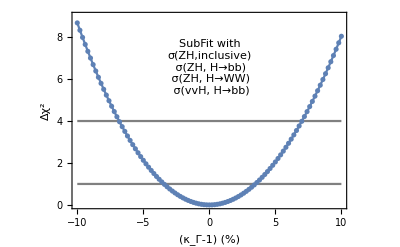

{{x→0.0348282}}

```mathematica
Show[Plot[{Interpolation[tempdata][x/100],1,4},{x,-0.1*100,0.1*100},PlotRange->{0,9},Frame->True,FrameLabel->{"(κ_Γ-1) (%)","Δχ^2"},BaseStyle->16,PlotStyle->{Automatic,Gray,Gray}],ListPlot[{#[[1]]*100,#[[2]]}&/@tempdata],Epilog->Inset[Framed[Style["SubFit with\nσ(ZH,inclusive)\n σ(ZH, H→bb)\n σ(ZH, H→WW)\n σ(vvH, H→bb)",13],FrameStyle->None,Background->White],Scaled[{0.5,0.72}]]]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

```mathematica
1/Sqrt[1/3.5^2+1/5.4^2]
```

2.93704

Tests

```mathematica
chisquare=(x^2/z)^2/dx^2+(y^2/z)^2/dy^2+x^4/dxp^2
```

x^4/dxp^2+x^4/(dx^2 z^2)+y^4/(dy^2 z^2)

```mathematica
{{D[chisquare,x,x],D[chisquare,x,y],D[chisquare,x,z]},
{D[chisquare,y,x],D[chisquare,y,y],D[chisquare,y,z]},
{D[chisquare,z,x],D[chisquare,z,y],D[chisquare,z,z]}}/2/.{x->1,y->1,z->1};
%//MatrixForm
```

(1/2 (12/dx^2+12/dxp^2) | 0 | -4/dx^2
0 | 6/dy^2 | -4/dy^2
-4/dx^2 | -4/dy^2 | 1/2 (6/dx^2+6/dy^2))

```mathematica
Inverse[%658]//Simplify;
%//MatrixForm
```

((dx^2 dxp^2 (dx^2+9 dy^2))/(6 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (4 dx^2 dxp^2 dy^2)/(3 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (2 dx^2 dxp^2 dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))
(4 dx^2 dxp^2 dy^2)/(3 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (dy^2 (9 dx^4+dxp^2 dy^2+9 dx^2 (dxp^2+dy^2)))/(6 (dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))) | (2 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2))
(2 dx^2 dxp^2 dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)) | (2 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)) | (3 dx^2 (dx^2+dxp^2) dy^2)/(dx^4+dxp^2 dy^2+dx^2 (dxp^2+9 dy^2)))

7-kappa deriving width for a random request from a senior member (really wasting time)

```mathematica
NSolve[kh[kz,kw,kg,kgamma,kb,kt,ktau]kappah==1,kb]
```

{{kb→-1/(√kappah)7.3035×10^-9 √(3.241×10^16-7.746×10^12 kappah-2.7743×10^15 kappah kg^2-7.45431×10^13 kappah kgamma^2-8.68589×10^14 kappah kt^2-2.07168×10^15 kappah ktau^2-7.00057×10^15 kappah kw^2-8.65348×10^14 kappah kz^2)},{kb→1/(√kappah)7.3035×10^-9 √(3.241×10^16-7.746×10^12 kappah-2.7743×10^15 kappah kg^2-7.45431×10^13 kappah kgamma^2-8.68589×10^14 kappah kt^2-2.07168×10^15 kappah ktau^2-7.00057×10^15 kappah kw^2-8.65348×10^14 kappah kz^2)}}

```mathematica
Module[{kappah},kappah=0.95;NMinimize[{chisquarecepc[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}]]
```

{4.82534,{kz→0.999106,kg→1.02916,kgamma→1.02834,kw→1.0274,kt→1.03051,ktau→1.02792}}

```mathematica
widthdata70=Table[{kappah,NMinimize[{chisquarecepc[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}][[1]]},{kappah,0.95,1.05,0.005}]
```

{{0.95,4.82534},{0.955,3.87901},{0.96,3.04191},{0.965,2.31162},{0.97,1.68578},{0.975,1.16209},{0.98,0.738316},{0.985,0.412298},{0.99,0.181927},{0.995,0.0451574},{1.,8.65073×10^-11},{1.005,0.0445222},{1.01,0.176845},{1.015,0.395143},{1.02,0.69764},{1.025,1.08261},{1.03,1.54838},{1.035,2.0933},{1.04,2.71581},{1.045,3.41435},{1.05,4.18742}}

```mathematica
NSolve[Interpolation[widthdata70][1+x]==1,{x,1.02}]
```

NSolve::ivar: 1.02 is not a valid variable.

NSolve[InterpolatingFunction[…][1+x]==1,{x,1.02}]

```mathematica
widthdata70L=Table[{kappah,NMinimize[{chisquarecepcL[{1/(√kappah)7.3035001988639674*^-9 √(3.2410041841*^16-7.746*^12 kappah-2.7742995815896*^15 kappah kg^2-7.45430962343*^13 kappah kgamma^2-8.685891213388*^14 kappah kt^2-2.071682284518561*^15 kappah ktau^2-7.000569037656*^15 kappah kw^2-8.653481171547*^14 kappah kz^2),kt,kg,kw,ktau,kz,kgamma},1],kg> 0,kg<2,kgamma>0,kgamma<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kt,ktau}][[1]]},{kappah,0.95,1.05,0.005}]
```

{{0.95,8.13819},{0.955,6.54393},{0.96,5.13311},{0.965,3.90178},{0.97,2.84613},{0.975,1.96245},{0.98,1.2471},{0.985,0.696577},{0.99,0.307432},{0.995,0.0763258},{1.,1.32684×10^-13},{1.005,0.0752819},{1.01,0.29908},{1.015,0.668383},{1.02,1.18026},{1.025,1.83184},{1.03,2.62034},{1.035,3.54305},{1.04,4.59732},{1.045,5.78057},{1.05,7.09028}}

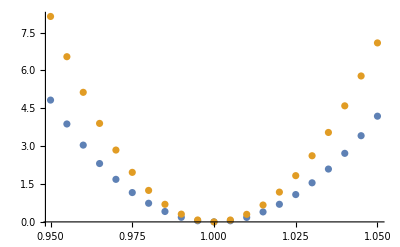

```mathematica
ListPlot[{widthdata70,widthdata70L}]
```

```mathematica
NSolve[Interpolation[widthdata70][1+x]==1,x]
NSolve[Interpolation[widthdata70L][1+x]==1,x]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.0232213}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.0179354}}

```mathematica
FindRoot[Interpolation[widthdata70][1+x]==1,{x,0}]
FindRoot[Interpolation[widthdata70L][1+x]==1,{x,0}]
```

InterpolatingFunction::dmval: Input value {11.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{x→0.024011}

InterpolatingFunction::dmval: Input value {11.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{x→0.0183896}